```mathematica
ClearAll[GraphPartion`FingerprintVectors]
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

Global`

```mathematica
SquareGrid[n_] := System`GridGraph[{n,n}, 
VertexLabels->If[n<10,Automatic,None],VertexWeight->Table[1/n/n,n*n], EdgeWeight->Automatic];
```

{4.44089×10^-16,1.,1.,2.,3.}

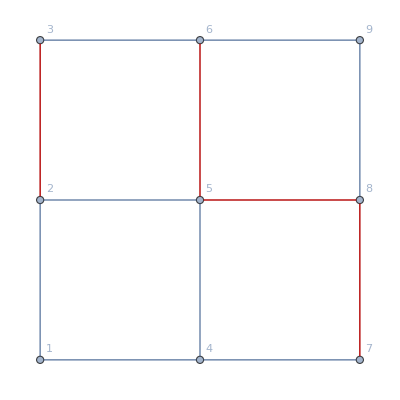
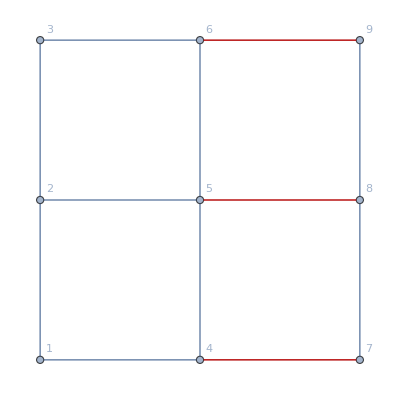
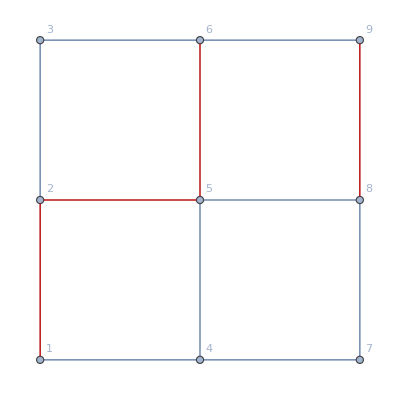
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
g= SquareGrid[3];
{ShowSpectralCut[g],ShowIsoperimetricCut[g], ShowMultipleFiedlerCut[g], ShowMultipleIsoperimetricCut[g]}
(*ShowMultipleFiedlerCut[g]*)
(*MultipleIsoperimetricVector[g];*)
```

```mathematica
v = MultipleIsoperimetricVector[g]
```

{J:,(5.56098 | 0.763158 | 0.711853 | 0.450571 | 0.0752495
0.763158 | 3.63238 | -0.816906 | -0.517065 | 0.574894
0.711853 | -0.816906 | 4.11068 | -0.351915 | 0.0867208
0.450571 | -0.517065 | -0.351915 | 4.44392 | -0.312079
0.0752495 | 0.574894 | 0.0867208 | -0.312079 | 3.56738)}

{{0.914603,-0.466362,0.447402,-0.055508,0.408481},{0.831283,0.265976,0.503045,-0.334017,0.126312},{0.845898,0.576979,0.255418,-1.5403,-0.0472316},{0.710846,-1.1094,0.617468,0.378786,0.804169},{0.446272,0.776612,1.03203,0.749544,0.131206},{0.811575,0.643838,-0.101701,-0.090505,0.160401},{0.882029,-0.773197,-0.00123418,0.488705,-1.48865},{0.823619,0.193779,-0.187251,0.585831,-0.32007},{0.855479,0.667224,-1.36684,0.675028,0.510747}}

{0,0,0,0,0,0,1,1,1}